```mathematica
$Assumptions = {x ∈ Reals, y ∈ Reals, θ ∈ Reals, ϵ ∈ Reals, κ ∈ Reals, ν ∈ Reals, ν >= 0, L ∈ Integers, L >= 0}
```

{x∈ℝ,y∈ℝ,θ∈ℝ,ϵ∈ℝ,κ∈ℝ,ν∈ℝ,ν≥0,L∈ℤ,L≥0}

## Preliminaries

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
H0 = FullSimplify[{{0, Δ, Δ*}, {Δ*, 0, Δ}, {Δ, Δ*, 0}}]
```

{{0,Δ,Conjugate[Δ]},{Conjugate[Δ],0,Δ},{Δ,Conjugate[Δ],0}}

```mathematica
δH = FullSimplify[{{0, α (ω q + ω* q*), α* (ω^2 q + ω^2* q*)}, {α* (ω q + ω* q*), 0, α (q + q*)}, {α (ω^2 q + ω^2* q*), α* (q + q*), 0}}]
```

{{0,(-1)^(1/3) α ((-1)^(1/3) q-Conjugate[q]),(-1)^(1/3) (-q+(-1)^(1/3) Conjugate[q]) Conjugate[α]},{(-1)^(1/3) ((-1)^(1/3) q-Conjugate[q]) Conjugate[α],0,2 α Re[q]},{(-1)^(1/3) α (-q+(-1)^(1/3) Conjugate[q]),2 Conjugate[α] Re[q],0}}

```mathematica
q =(x + I y)
```

x+ⅈ y

```mathematica
H = FullSimplify[δH + H0]
```

{{0,-((x+√3 y) α)+Δ,(-x+√3 y) Conjugate[α]+Conjugate[Δ]},{-((x+√3 y) Conjugate[α])+Conjugate[Δ],0,2 x α+Δ},{-x α+√3 y α+Δ,2 x Conjugate[α]+Conjugate[Δ],0}}

## Characteristic Polynomial

```mathematica
poly = FullSimplify[CharacteristicPolynomial[H, λ]]
```

(2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2)-λ^3+6 (x^2+y^2) α λ Conjugate[α]+2 x (x^2-3 y^2) Conjugate[α]^3+3 Δ λ Conjugate[Δ]-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3

```mathematica
b = -FullSimplify[ComplexExpand[6 α Conjugate[α] (x^2+y^2) + 3 Δ Conjugate[Δ], {α, Δ}]]
c = -FullSimplify[ComplexExpand[4 Re[α^3] x^3 - 6 Re[α^2 Δ] x^2 - 6 Re[α^2 Δ] y^2 - 12 Re[α^3] x y^2 + 2 Re[Δ^3], {α, Δ}]]
dis = FullSimplify[4 b^3 + 27 c^2]
```

-6 (x^2+y^2) α Conjugate[α]-3 Δ Conjugate[Δ]

-((2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2))-2 x (x^2-3 y^2) Conjugate[α]^3+3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]-Conjugate[Δ]^3

27 (-4 (Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α])^3+((2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2)+2 x (x^2-3 y^2) Conjugate[α]^3-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3)^2)

## Eigenvalues

```mathematica
ϵ0 = FullSimplify[2 Sqrt[-b/3] Cos[1/3 ArcCos[(3 c)/(2 b) * Sqrt[-3/b]] - 0 * 2 π/3]]
ϵ1 = FullSimplify[2 Sqrt[-b/3] Cos[1/3 ArcCos[(3 c)/(2 b) * Sqrt[-3/b]] - 1 * 2 π/3]]
ϵ2 = FullSimplify[2 Sqrt[-b/3] Cos[1/3 ArcCos[(3 c)/(2 b) * Sqrt[-3/b]] - 2 * 2 π/3]]
```

2 √(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Cos[1/3 ArcCos[1/2 (1/(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]))^(3/2) ((2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2)+2 x (x^2-3 y^2) Conjugate[α]^3-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3)]]

-2 √(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Cos[1/3 (π+ArcCos[1/2 (1/(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]))^(3/2) ((2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2)+2 x (x^2-3 y^2) Conjugate[α]^3-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3)])]

-2 √(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]) Sin[1/6 (π+2 ArcCos[1/2 (1/(Abs[Δ]^2+2 (x^2+y^2) α Conjugate[α]))^(3/2) ((2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2)+2 x (x^2-3 y^2) Conjugate[α]^3-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3)])]

```mathematica
FullSimplify[Sin[2 π/3 2]]
```

-(√3)/2

```mathematica
α = 1 + 3 I
Δ = 1 + 23 I
y = 1.23
x = 1
```

1+3 ⅈ

1+23 ⅈ

1.23

1

```mathematica
temp[λ_] := (2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2)-λ^3+6 (x^2+y^2) α λ Conjugate[α]+2 x (x^2-3 y^2) Conjugate[α]^3+3 Δ λ Conjugate[Δ]-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3
```

```mathematica
FullSimplify[ϵ0]
FullSimplify[ϵ1]
FullSimplify[ϵ2]
```

41.5484+0. ⅈ

0.346235+0. ⅈ

-41.8946+0. ⅈ

```mathematica
FullSimplify[-c]
```

-602.675+0. ⅈ

## Eigenvector Entries

```mathematica
tA1 = 1
tA5 = FullSimplify[ComplexExpand[1/(ϵ^2 - (Conjugate[Δ] + Conjugate[α] (q + Conjugate[q])) (Δ + α (q + Conjugate[q])))(ϵ (Δ + α (Conjugate[ω] q + ω Conjugate[q])) + (Conjugate[Δ] + Conjugate[α] (q + Conjugate[q])) (Conjugate[Δ] + Conjugate[α] (ω q + Conjugate[ω] Conjugate[q]))),{α, Δ}]]
tA3 = FullSimplify[ComplexExpand[1/(Δ + α (ω q + Conjugate[ω] Conjugate[q])) (ϵ - (Conjugate[Δ] + Conjugate[α] (Conjugate[ω] q + ω Conjugate[q])) * 1/(ϵ^2 - (Conjugate[Δ] + Conjugate[α] (q + Conjugate[q])) (Δ + α (q + Conjugate[q])))(ϵ (Δ + α (Conjugate[ω] q + ω Conjugate[q])) + (Conjugate[Δ] + Conjugate[α] (q + Conjugate[q])) (Conjugate[Δ] + Conjugate[α] (ω q + Conjugate[ω] Conjugate[q])))),{α, Δ}]]
```

1

((-x α+√3 y α+Δ) ϵ-((x+√3 y) Conjugate[α]-Conjugate[Δ]) (2 x Conjugate[α]+Conjugate[Δ]))/(ϵ^2-(2 x α+Δ) (2 x Conjugate[α]+Conjugate[Δ]))

(2 x (x+√3 y) (x^2-3 y^2) Conjugate[α]^4-(5 x^3+3 √3 x^2 y-3 x y^2+3 √3 y^3) Conjugate[α]^3 Conjugate[Δ]+Conjugate[α]^2 ((5 x^3 α+3 y^2 (√3 y α+Δ)+x^2 (3 √3 y α+Δ)+x y (-3 y α+2 √3 Δ)) ϵ+3 (x^2+y^2) Conjugate[Δ]^2)-Conjugate[Δ] (-ϵ^3+(x α+√3 y α+2 Δ) ϵ Conjugate[Δ]+Conjugate[Δ]^3)+Conjugate[α] (-((x+√3 y) ϵ^3)+Conjugate[Δ] (-4 x (x-√3 y) α ϵ+(x+√3 y) (Δ ϵ+Conjugate[Δ]^2))))/((Abs[Δ]^2+((x^2+2 √3 x y+3 y^2) α-(x+√3 y) Δ) Conjugate[α]-(x+√3 y) α Conjugate[Δ]) (ϵ^2-(2 x α+Δ) (2 x Conjugate[α]+Conjugate[Δ])))

```mathematica
nmz = ComplexExpand[Sqrt[tA1 * Conjugate[tA1] + tA3 * Conjugate[tA3] + tA5 * Conjugate[tA5]] {α, Δ}]
```

{α Cos[1/2 Arg[1+1/1+((-(((x+√3 y) Conjugate[α]-Conjugate[Δ]) (1))+1) (1))/((-((2 x α+Δ) (1))+4 (1) (Cos11])^2) (1))]] ((1+3+((1) 1)/(1+1))^2)^(1/4)+ⅈ α 1 1,1}
 |  |  |  |

```mathematica
A1 = tA1/nmz
A3 =tA3/nmz
A5 = tA5/nmz
```

{1/(α Cos[1/2 Arg[1+1/1+((1) 1)/((1) 1)]] ((1+3+1)^2)^(1/4)+1),1/(Δ Cos[1/2 Arg[1]] ((((11)^2))^(1/4)+1)}
 |  |  |  |

{(6+Conjugate[α] (-8 (x+√3 y) (1)^(3/2) Cos[1/3 1]^3+1 1))/((Abs[Δ]^2+((x^2+2 √3 x y+3 y^2) α-(x+√3 y) Δ) Conjugate[α]-(x+√3 y) α Conjugate[Δ]) (1) (α Cos[1/2 Arg[1]] (1^2)^(1/4)+1)),1/1}
 |  |  |  |

{(-(((x+√3 y) Conjugate[α]-Conjugate[Δ]) (2 x Conjugate[α]+Conjugate[Δ]))+2 (1) 1 Cos[1/3 ArcCos[3/2 √3 1 (1)]])/((-((2 x α+Δ) (2 x Conjugate[α]+Conjugate[Δ]))+4 (Abs[Δ]^2+1/3 (x^2+y^2) α Conjugate[α]) Cos[1]^2) (1)),(-(1)+1)/((1) 1)}
 |  |  |  |

## Derivatives

```mathematica
ϵ = ϵ0
```

2 √(Abs[Δ]^2+1/3 (x^2+y^2) α Conjugate[α]) Cos[1/3 ArcCos[3/2 √3 (1/((x^2+y^2) α Conjugate[α]+3 Δ Conjugate[Δ]))^(3/2) ((2 x α+Δ) ((x^2-3 y^2) α^2-2 x α Δ+Δ^2)+2 x (x^2-3 y^2) Conjugate[α]^3-3 (x^2+y^2) Conjugate[α]^2 Conjugate[Δ]+Conjugate[Δ]^3)]]

```mathematica
dxA1 = tA1 * D[1/nmz, x] + 1/nmz * D[tA1, x]
dxA3 = tA3 * D[1/nmz, x] + 1/nmz * D[tA3, x]
dxA5 = tA5 * D[1/nmz, x] + 1/nmz * D[tA5, x]
dyA1 = tA1 * D[1/nmz, y] + 1/nmz * D[tA1, y]
dyA3 = tA3 * D[1/nmz, y] + 1/nmz * D[tA3, y]
dyA5 = tA5 * D[1/nmz, y] + 1/nmz * D[tA5, y]
```

{-((α 2 (1/(3 1)+24+1))/(2 (1^2)^(3/4))+1/(2 1)+1-1/2 4 (1))/((α Cos[1/2 Arg[1]] (1^2)^(1/4)+1)^2),-(1/(2 1)+4)/(1)^2}
 |  |  |  |

{(-(((1-Δ) 1-α 1) (1))/((1)^2 (-((1) 1)+1))-1+1/1)/(α Cos[1/2 Arg[1+1/1+((1) 1)/((1) 1)]] ((1+3+1)^2)^(1/4)+1)-1,1}
 |  |  |  |

{(1/(-((2 x α+Δ) (1+1))+1)-((-1+1)11)/(1)^2)/(α Cos[1/2 Arg[1+1/1+((1) 1)/((1) 1)]] ((1+3+1)^2)^(1/4)+1)-1/1,1/1-1}
 |  |  |  |

{-((α 2 (1/(3 1)+24+1))/(2 (1^2)^(3/4))+1/(2 1)+1-1/2 4 (1))/((α Cos[1/2 Arg[1]] (1^2)^(1/4)+1)^2),-(1/(2 1)+4)/(1)^2}
 |  |  |  |

{(-(((1-1) 1-1) 1)/((1)^2 (-((1) 1)+1))-1+1)/(α Cos[1/2 Arg[1+1/1+((1) 1)/((1) 1)]] ((1+3+1)^2)^(1/4)+1)-1/1,1}
 |  |  |  |

{((-√3 Conjugate[α] (2 x 1+1)+3)/(-((2 x α+Δ) (1+1))+1)-1/1^2)/(α Cos[1/2 Arg[1+1/1+((1) 1)/((1) 1)]] ((1+3+1)^2)^(1/4)+1)-1/1,1-1}
 |  |  |  |

```mathematica
x = 0
y = 0
```

0

0

## RMG Results

```mathematica
κ = 1
L = 3
```

1

3

```mathematica
Clear[L]
```

```mathematica
Δ = FullSimplify[ComplexExpand[((1 - ν^2 κ^2) (1 - (ω ν^2 κ^2)^L))/((1 - ω ν^2 κ^2) (1 - (ν^2 κ^2)^L))]]
```

(2+ⅈ (ⅈ+√3) ν^2+(-1-ⅈ √3) ν^4+2 ν^6+ⅈ (ⅈ+√3) ν^8)/(2 (1+ν^2+ν^4+ν^6+ν^8))

```mathematica
delt[ν_, L_] :=FullSimplify[ComplexExpand[((1 - ν^2 κ^2) (1 - (ω ν^2 κ^2)^L))/((1 - ω ν^2 κ^2) (1 - (ν^2 κ^2)^L))]]
```

```mathematica
α = FullSimplify[ComplexExpand[(-(1 - ν^2 κ^2))/(κ (1 - (ν^2 κ^2)^L)) * ((2 Conjugate[ω] (ω ν^2 κ^2 - L (ω ν^2 κ^2)^L + (L - 1) (ω ν^2 κ^2)^(L + 1)))/((1 - ω ν^2 κ^2)^2) + ((1 - ν^2 κ^2) (1 - (ω ν^2 κ^2)^L)(ν^2 κ^2 - L (ν^2 κ^2)^L + (L - 1) (ν^2 κ^2)^(L + 1)))/((1 - ν^2 κ^2)^2 (1 - (ν^2 κ^2)^L) (1 - ω ν^2 κ^2)))]]
```

(ν^2 (-6+(-3-5 ⅈ √3) ν^2+(3-5 ⅈ √3) ν^4+(6-2 ⅈ √3) ν^6))/(2 (1+ν^2+ν^4)^2)

```mathematica
alph[ν_, L_] := FullSimplify[ComplexExpand[(-(1 - ν^2 κ^2))/(κ (1 - (ν^2 κ^2)^L)) * ((2 Conjugate[ω] (ω ν^2 κ^2 - L (ω ν^2 κ^2)^L + (L - 1) (ω ν^2 κ^2)^(L + 1)))/((1 - ω ν^2 κ^2)^2) + ((1 - ν^2 κ^2) (1 - (ω ν^2 κ^2)^L)(ν^2 κ^2 - L (ν^2 κ^2)^L + (L - 1) (ν^2 κ^2)^(L + 1)))/((1 - ν^2 κ^2)^2 (1 - (ν^2 κ^2)^L) (1 - ω ν^2 κ^2)))]]
```

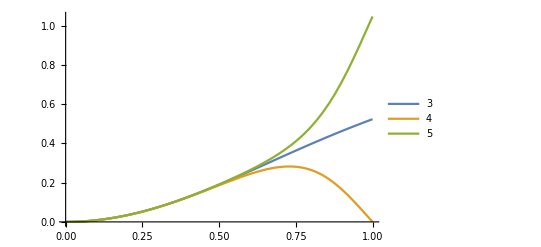

```mathematica
Plot[{Arg[delt[ν, 3]], Arg[delt[ν, 4]], Arg[delt[ν, 5]]}, {ν, 0, 1}, PlotLegends->{3, 4, 5}]
```

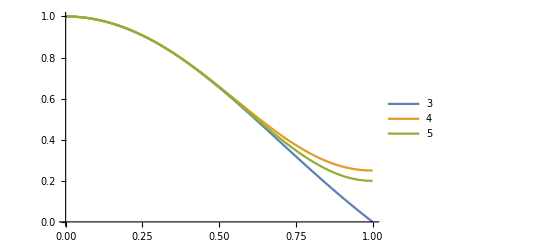

```mathematica
Plot[{Abs[delt[ν, 3]], Abs[delt[ν, 4]], Abs[delt[ν, 5]]}, {ν, 0, 1}, PlotLegends->{3, 4, 5}]
```

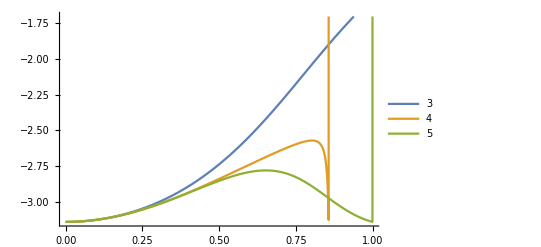

```mathematica
Plot[{Arg[alph[ν, 3]], Arg[alph[ν, 4]], Arg[alph[ν, 5]]}, {ν, 0, 1}, PlotLegends->{3, 4, 5}]
```

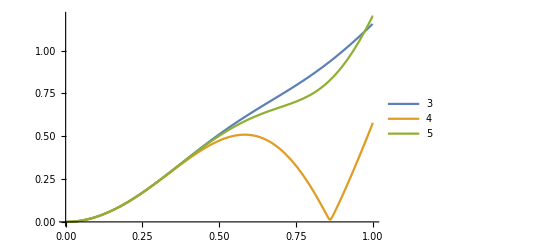

```mathematica
Plot[{Abs[alph[ν, 3]], Abs[alph[ν, 4]], Abs[alph[ν, 5]]}, {ν, 0, 1}, PlotLegends->{3, 4, 5}]
```

```mathematica
Clear[α, Δ, x, y, ϵ]
```